## Length Distribution looping, <k> = 4, n=2000, D=1..6

### Predicted

```mathematica
clist={3.91006469727*10^-7,0.000122680664062,0.000608520507813,0.001376953125,0.002392578125,0.003642578125};
```

```mathematica
n=2000;
m=4000;
d=3;
c=clist[[d]];
```

```mathematica
A[s_]:=(Sqrt[2^(d+1)*d])/(d-1)!*(Sqrt[2]*s)^(d-1);
```

```mathematica
NetA[s_]:=If[s≤ 0.5,A[s],A[s]-A[0.5*d*((s-0.5)/(0.5*d-0.5))]]
```

```mathematica
unNormSigma[s_]:=c*n^2/(2*m)*NetA[s]/(s^2+c)
```

```mathematica
constant=Integrate[unNormSigma[s],{s,0,0.5*d}];
```

```mathematica
sigma[s_]:=unNormSigma[s]/constant;
```

```mathematica
Integrate[sigma[s],{s,0,0.5*d}]
```

1.

### Observed

```mathematica
data=Import["C:\\Users\\Gateway\\Dropbox\\RMath\\Summer\\opinion_model\\data\\length_Distro_3D.dat","FieldSeparators" -> ","];
```

```mathematica
observed = Histogram[data];
```

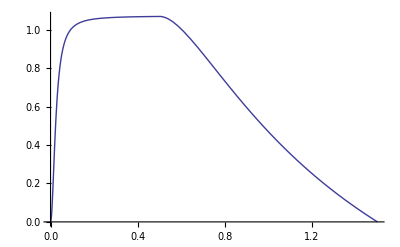

```mathematica
expected = Plot[{sigma[s]},{s,0,0.5*d},PlotRange-> {{0,0.5*d},{0,Full}}]
```

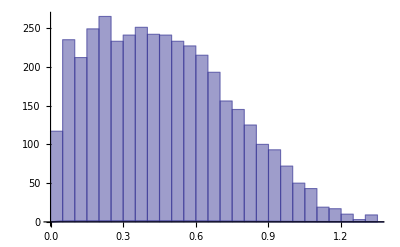

```mathematica
Show[observed, expected]
```

## Geometric Distance

### http://en.wikipedia.org/wiki/Sphere#Generalization_to_other_dimensions

```mathematica
(*ACircle[s_,d_]:=If[d==1,2,If[EvenQ[d],(2*Pi)^(d/2)*s^(d-1)/((d/2-1)!*2^(d/2-1)),2*(2*Pi)^((d-1)/2)*s^(d-1)/((d-2)!/(((d-1)/2-1)!*2^((d-1)/2-1)))]]*)
```

```mathematica
(*f[s_]:=c*n^2/(2*m)*ACircle[s,d]/(s^2+c)*)
```